# Tips & Tricks: Mathematica for Research

## Lecture 1 (13/04/2026)

## Functions

```mathematica
<<Notation`
```

```mathematica
Notation[Subscript[γ, a_] ⟺ γ[a_]]
Notation[Subscript[g, a_ b_] ⟺ g[a_,b_]]
```

```mathematica
NumQ[_?NumericQ]=True;
NumQ[g[a_,b_]]=True;
NumQ[𝕕]=True;
NumQ[_]=False;
```

```mathematica
ClearAll[CenterDot]
SetAttributes[CenterDot,{Flat}]
CenterDot/:c___·(a1_+a2_)·d___:=c·a1·d+c·a2·d
CenterDot/:a1_·a2_:=a1 a2/;NumQ[a1]||NumQ[a2]
CenterDot/:c___·(num_ a1_)·d___:=num c·a1·d/;NumQ[num]
CenterDot/:num_·a1_:=num CenterDot[a1]/;NumQ[num]
```

```mathematica
ClearAll[g]
SetAttributes[g,{Orderless}]
g/:g[a_,b_]c_:=(c/.b->a)/;Not@FreeQ[c,b]
g/:g[a_,a_]:=𝕕
```

```mathematica
rules={
c___·γ[a_]·γ[b_]·d___:>c·(-γ[b]·γ[a]+2g[a,b])·d/;Not@OrderedQ[{a,b}],
c___·γ[a_]·γ[a_]·d___:>c·(g[a,a])·d
};
GammaAlgebra[exp_]:=(exp//.rules//Simplify)
```

## Example

```mathematica
γ[d]·γ[a]·γ[c]·γ[b]·γ[d]·γ[c]·γ[a]//GammaAlgebra
```

-((-16+24 𝕕-10 𝕕^2+𝕕^3) γ_b)

## Other stuff

```mathematica
γ[a]g[c,d]
```

g_(c d) γ_a

```mathematica
a·b
```

```mathematica
MatchQ[γ[a]·γ[b],c_·γ[a]·γ[b]]
```

True

```mathematica
Clear[f]
```

```mathematica
c=2;
f[x_]:=x^2+c
```

```mathematica
f[1]
f[2]
```

3

6

```mathematica
c=10;
```

```mathematica
f[1]
```

11

```mathematica
?f
```

```mathematica
?Times
```

```mathematica
NumQ[_?NumericQ]=True
NumQ[g[a_,b_]]=True
NumQ[𝕕]=True
NumQ[_]=False
```

True

True

True

False

```mathematica
NumQ[g[a,a]]
```

```mathematica
NumQ[𝕕]
```

True

```mathematica
ClearAll[CenterDot]
SetAttributes[CenterDot,{Flat}]
CenterDot/:c___·(a1_+a2_)·d___:=c·a1·d+c·a2·d
CenterDot/:a1_·a2_:=a1 a2/;NumQ[a1]||NumQ[a2]
CenterDot/:c___·(num_ a1_)·d___:=num c·a1·d/;NumQ[num]
CenterDot/:num_·a1_:=num CenterDot[a1]/;NumQ[num]
```

```mathematica
ClearAll[g]
SetAttributes[g,{Orderless}]
g/:g[a_,b_]c_:=(c/.b->a)/;Not@FreeQ[c,b]
g/:g[a_,a_]:=𝕕
```

```mathematica
g[a,b]f[a]
g[a,b]f[b]
```

f[b]

f[a]

```mathematica
g[a,b]+g[b,a]
```

g[a,b]+g[b,a]

```mathematica
Not@FreeQ[γ[c],c]
```

True

```mathematica
rule={
c___·γ[a_]·γ[b_]·d___:>c·(-γ[b]·γ[a]+2g[a,b])·d/;Not@OrderedQ[{a,b}],
c___·γ[a_]·γ[a_]·d___:>c·(g[a,a])·d
};
```

```mathematica
γ[a]·(2γ[b])·γ[d]
```

2 γ[a]·γ[b]·γ[d]

```mathematica
g[μ,d]γ[μ]
```

g[μ,d] γ[μ]

```mathematica
γ[c]·γ[μ]·γ[d]·γ[ν]·γ[μ]/.rule
```

γ[c]·2·γ[ν]·γ[d]-γ[c]·(γ[d]·γ[μ])·γ[ν]·γ[μ]

```mathematica
c·γ[a]·γ[a]·d/.rule
```

c·g[a,a]·d

```mathematica
NumericQ[√2]
```

True

```mathematica
Sqrt[2]//FullForm
```

Power[2,Rational[1,2]]

```mathematica
NumberQ[π//N]
```

True

```mathematica
c·(γ[a]+γ[b])·d
```

c·γ[a]·d+c·γ[b]·d

```mathematica
γ[a]·γ[b]+γ[b]·γ[a]/.rule
```

CenterDot[-γ[a]·γ[b]+2 g[b,a]]+γ[a]·γ[b]

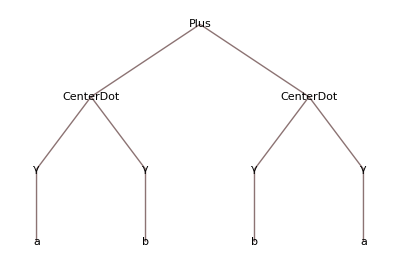

```mathematica
γ[a]·γ[b]+γ[b]·γ[a]//TreeForm
```

```mathematica
??Plus
```

```mathematica
?CenterDot
```

```mathematica
a b + b a
```

2 a b

```mathematica
Clear[rule]
```

```mathematica
rule
```

rule

```mathematica
γ[d]·γ[a]·γ[c]·γ[b]·γ[d]·γ[c]·γ[a]//.rule//Simplify
```

-((-16+24 𝕕-10 𝕕^2+𝕕^3) γ[b])

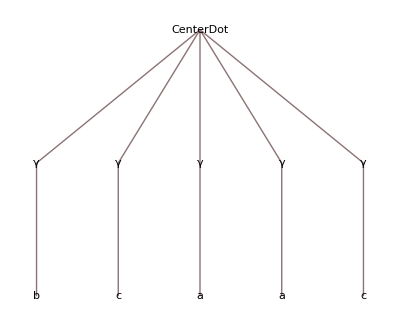

```mathematica
(γ[b]·γ[c])·γ[a]·(γ[a]·γ[c])//TreeForm
```

```mathematica
g[a,b]·γ[b]
```

γ[a]